```mathematica
ClearAll["Global`*"]
```

```mathematica
L:=1
m:=0.1 (*m=4 очень интересный случай*)
r0:=√((4 L^5)/(3m))
R0:=√((3m L^5)/4)
zL:=0
zR:=0
eps:=10^-10
```

```mathematica
bcsLeft={
r[zL]==r0,
a[zL]==0+eps
};
```

```mathematica
equations={
r'[z]==((8 L^5)/(3 r[z])-2m r[z])Cos[a[z]],
a'[z]==((8 L^5)/(3 r[z]^2)+2m)Sin[a[z]]
};
```

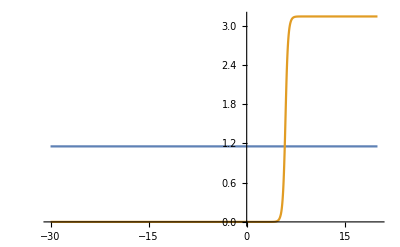

```mathematica
zR:=20;
sol=NDSolveValue[Join[equations, bcsLeft], {r, a}, {z, zL-30, zR},Method->"StiffnessSwitching",WorkingPrecision->30,MaxSteps->100000,PrecisionGoal->15,AccuracyGoal->15];
Plot[{sol[[1]][z], sol[[2]][z]}, {z, zL-30, zR}, PlotRange->Full]
```

```mathematica
sol[[1]][1]
```

1.154700538379251529018297561

```mathematica
sol[[1]][3]
```

1.154700538379251529018297561

```mathematica
f[z_]:=((8 L^5)/(3 r[z])-2m r[z])Cos[a[z]]/.{r[z]->sol[[1]][z],a[z]->sol[[2]][z]}
```

```mathematica
f[0]
```

0.

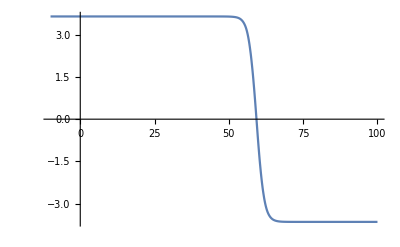

```mathematica
Plot[Re[sol[[1]][z]Exp[I sol[[2]][z]]], {z, -10, 100}]
```